```mathematica
L=0.1;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

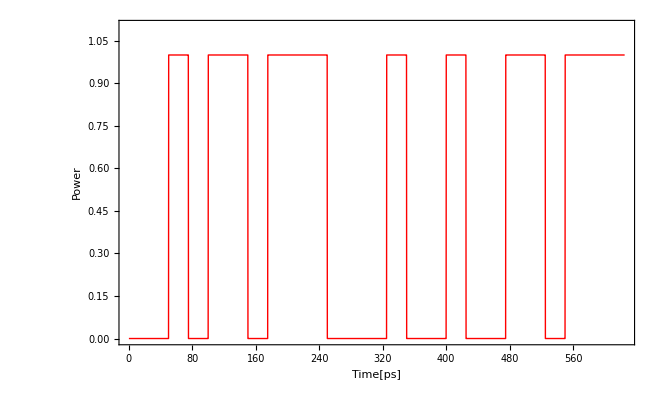

```mathematica
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;
rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->30},PlotRange->{0,1.1}]
```

1/2 (1+Cos[56000000000 π t])

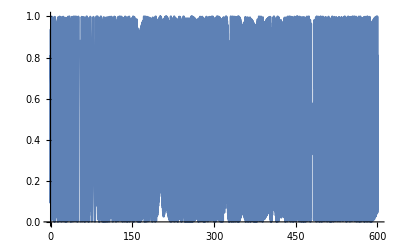

```mathematica
Fc= 28*10^9;(*搬送波の周波数[THz]*)
carrier[t_]= (Cos[2*Pi*Fc*t]+1)/2
Plot[carrier[t], {t,0,600}]
```

```mathematica
cs[t_]=signal[t]*carrier[t]
```

Cos[400 π t] (If[1/40000000000<t<1/20000000000,0,0]+If[1/20000000000<t<3/40000000000,1,0]+If[3/40000000000<t<1/10000000000,0,0]+If[1/10000000000<t<1/8000000000,1,0]+If[1/8000000000<t<3/20000000000,1,0]+If[3/20000000000<t<7/40000000000,0,0]+If[7/40000000000<t<1/5000000000,1,0]+If[1/5000000000<t<9/40000000000,1,0]+If[9/40000000000<t<1/4000000000,1,0]+If[1/4000000000<t<11/40000000000,0,0]+If[11/40000000000<t<3/10000000000,0,0]+If[3/10000000000<t<13/40000000000,0,0]+If[13/40000000000<t<7/20000000000,1,0]+If[7/20000000000<t<3/8000000000,0,0]+If[3/8000000000<t<1/2500000000,0,0]+If[1/2500000000<t<17/40000000000,1,0]+If[17/40000000000<t<9/20000000000,0,0]+If[9/20000000000<t<19/40000000000,0,0]+If[19/40000000000<t<1/2000000000,1,0]+If[1/2000000000<t<21/40000000000,1,0]+If[21/40000000000<t<11/20000000000,0,0]+If[11/20000000000<t<23/40000000000,1,0]+If[23/40000000000<t<3/5000000000,1,0]+If[3/5000000000<t<1/1600000000,1,0]+If[1/1600000000<t<13/20000000000,1,0])

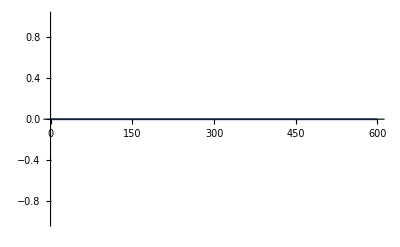

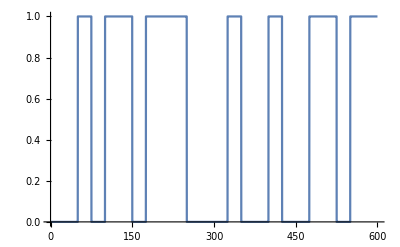

```mathematica
Plot[cs[t], {t, 0, 600}]
Plot[signal[t],{t,0,600}]
```

```mathematica
∫_0^(bit*25*10^-12) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

(ⅇ^(-(ⅈ f π)/800000000) (-3136000000000000000000 ⅈ+8 ⅈ ⅇ^((3 ⅈ f π)/4000000000) (-392000000000000000000+f^2)+ⅇ^((ⅈ f π)/5000000000) (-3136000000000000000000 ⅈ+28000000000 √(2 (5+√5)) f-ⅈ (-5+√5) f^2)+ⅇ^((3 ⅈ f π)/10000000000) (3136000000000000000000 ⅈ+28000000000 √(2 (5+√5)) f+ⅈ (-5+√5) f^2)+ⅇ^((3 ⅈ f π)/20000000000) (3136000000000000000000 ⅈ+28000000000 √(10-2 √5) f+ⅈ (-3+√5) f^2)+ⅇ^((23 ⅈ f π)/20000000000) (3136000000000000000000 ⅈ+28000000000 √(10-2 √5) f+ⅈ (-3+√5) f^2)+ⅇ^((21 ⅈ f π)/20000000000) (3136000000000000000000 ⅈ-28000000000 √(2 (5+√5)) f-ⅈ (3+√5) f^2)+ⅇ^((9 ⅈ f π)/20000000000) (3136000000000000000000 ⅈ+28000000000 √(2 (5+√5)) f-ⅈ (3+√5) f^2)+ⅇ^((19 ⅈ f π)/20000000000) (-3136000000000000000000 ⅈ-28000000000 √(2 (5+√5)) f+ⅈ (3+√5) f^2)+ⅇ^((11 ⅈ f π)/20000000000) (-3136000000000000000000 ⅈ+28000000000 √(2 (5+√5)) f+ⅈ (3+√5) f^2)+ⅇ^((9 ⅈ f π)/10000000000) (3136000000000000000000 ⅈ-28000000000 √(10-2 √5) f-ⅈ (5+√5) f^2)+ⅇ^((3 ⅈ f π)/5000000000) (3136000000000000000000 ⅈ+28000000000 √(10-2 √5) f-ⅈ (5+√5) f^2)+ⅇ^((11 ⅈ f π)/10000000000) (-3136000000000000000000 ⅈ-28000000000 √(10-2 √5) f+ⅈ (5+√5) f^2)+ⅇ^((ⅈ f π)/2500000000) (-3136000000000000000000 ⅈ+28000000000 √(10-2 √5) f+ⅈ (5+√5) f^2)))/(16 (-28000000000+f) f (28000000000+f) π)

```mathematica
fc[f_]:=(ⅇ^(-(ⅈ f π)/800000000) (-3136000000000000000000 ⅈ+8 ⅈ ⅇ^((3 ⅈ f π)/4000000000) (-392000000000000000000+f^2)+ⅇ^((ⅈ f π)/5000000000) (-3136000000000000000000 ⅈ+28000000000 √(2 (5+√5)) f-ⅈ (-5+√5) f^2)+ⅇ^((3 ⅈ f π)/10000000000) (3136000000000000000000 ⅈ+28000000000 √(2 (5+√5)) f+ⅈ (-5+√5) f^2)+ⅇ^((3 ⅈ f π)/20000000000) (3136000000000000000000 ⅈ+28000000000 √(10-2 √5) f+ⅈ (-3+√5) f^2)+ⅇ^((23 ⅈ f π)/20000000000) (3136000000000000000000 ⅈ+28000000000 √(10-2 √5) f+ⅈ (-3+√5) f^2)+ⅇ^((21 ⅈ f π)/20000000000) (3136000000000000000000 ⅈ-28000000000 √(2 (5+√5)) f-ⅈ (3+√5) f^2)+ⅇ^((9 ⅈ f π)/20000000000) (3136000000000000000000 ⅈ+28000000000 √(2 (5+√5)) f-ⅈ (3+√5) f^2)+ⅇ^((19 ⅈ f π)/20000000000) (-3136000000000000000000 ⅈ-28000000000 √(2 (5+√5)) f+ⅈ (3+√5) f^2)+ⅇ^((11 ⅈ f π)/20000000000) (-3136000000000000000000 ⅈ+28000000000 √(2 (5+√5)) f+ⅈ (3+√5) f^2)+ⅇ^((9 ⅈ f π)/10000000000) (3136000000000000000000 ⅈ-28000000000 √(10-2 √5) f-ⅈ (5+√5) f^2)+ⅇ^((3 ⅈ f π)/5000000000) (3136000000000000000000 ⅈ+28000000000 √(10-2 √5) f-ⅈ (5+√5) f^2)+ⅇ^((11 ⅈ f π)/10000000000) (-3136000000000000000000 ⅈ-28000000000 √(10-2 √5) f+ⅈ (5+√5) f^2)+ⅇ^((ⅈ f π)/2500000000) (-3136000000000000000000 ⅈ+28000000000 √(10-2 √5) f+ⅈ (5+√5) f^2)))/(16 (-28000000000+f) f (28000000000+f) π)
```

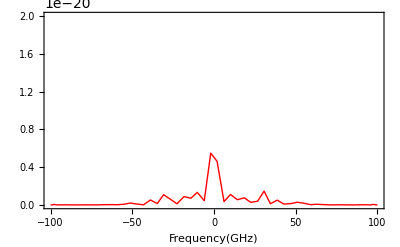

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-100,100},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(GHz)"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```